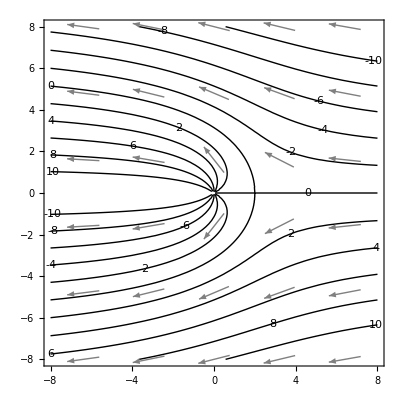

```mathematica
ClearAll["Global`*"]
u=-2+(4 x)/(x^2+y^2);
v=(4 y)/(x^2+y^2);
ψ[x_,y_]=-2 y+4 ArcTan[x,y-2 π];
list={{7,0},{7,2.2},{7,4.3}};

a=ContourPlot[ψ[x,y],{x,-8,8},{y,-8,8},ContourShading->None,Frame->True,Axes->True,ContourLabels->True,ContourStyle->Thin,Contours->Table[n,{n,-10,10,2}]];
b=VectorPlot[{u,v},{x,-8,8},{y,-8,8},VectorColorFunction->None,VectorStyle->{Thick,Gray},VectorScale->{0.07,Scaled[0.7],None},VectorPoints->{5,6}];
Show[{a,b}]
```